# UniDyn--Demo-07.nb

Aritro Sinha Roy
as836@cornell.edu
Cornell University

Abstract:  This demonstration notebook loads the UniDyn package and illustrate its use in simulating a three pulse experiment with phase-cycling for selective generation of specific quantum coherence orders using a system of three spin-1/2 particles.

## Set the path to the package

Tell Mathematica the path to the directory containing the package.    

EDIT THE FOLLOWING PATH STRING:

```mathematica
$UniDynPath ="C:/Users/as836/Documents/Work_with_John/UniDyn-master/unidyn";
```

YOU SHOULD NOT NEED TO EDIT ANYTHING FROM HERE ONWARDS.

## Load the package

Append the package path to the system path.  Before trying to load the package, ask Mathematica to find it.  This is a test that we directed Mathematica to the correct directory.  The output of this command should be the full system path to the UniDyn.m file.

```mathematica
(* $Path = AppendTo[$Path,$NCPath];*)
$Path = AppendTo[$Path,$UniDynPath];
FindFile["UniDyn`"]
```

C:\Users\as836\Documents\Work_with_John\UniDyn-master\unidyn\UniDyn.m

Now that we are confident that the path is set correctly, load the package.  Setting the global $VerboseLoad variable to True will print out the help strings for key commands in the package.

```mathematica
$VerboseLoad =True; (* Set to load quietly *)
Needs["UniDyn`"]
```

Run the unit tests .

```mathematica
SetDirectory[$UniDynPath];
test$report =TestReport /@ FileNames["*-tests.m"];
TableForm[Table[test$report [[k]],{k,1,Length[test$report]}]]
```

TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]

## Three spin-1/2 particles: Selective quantum coherence generation

Create a system of three spin-1/2 particles.

```mathematica
Needs["UniDyn`"];
Clear[Ix1, Iy1, Iz1,Δ1,Ix2, Iy2, Iz2,Δ2,Ix3, Iy3, Iz3,Δ3,a12,a13,a23]
Quiet[
CreateScalar[{Δ1,Δ2,Δ3,a12,a13,a23}];
CreateOperator[{{Ix1, Iy1, Iz1},{Ix2,Iy2,Iz2},{Ix3,Iy3,Iz3}}];
SpinSingle$CreateOperators[Ix1, Iy1, Iz1, 1/2];
SpinSingle$CreateOperators[Ix2, Iy2, Iz2, 1/2];
SpinSingle$CreateOperators[Ix3, Iy3, Iz3, 1/2];
]
```

Define some useful functions to extract operators

```mathematica
(* Extraction of operators from an expression *)
op$extA[elem_]:=Module[{pos,ans},
pos=Position[OperatorQ/@Level[elem,1],True];
ans=Level[elem,1][[pos[[1,1]]]];
Return[ans];
];

op$ext[elem_]:=Module[{ans},
If[Dimensions[elem]==={},ans = elem,
ans = Check[op$extA[elem],If[OperatorQ@elem,elem,None]]//Quiet];
Return[ans];
];

(* Group and simplify expressions by operators *)
col$op[exp_,op_,s_]:= Module[{op$l,exp$l,dim,exp$s,j},exp$l = exp//Expand;dim = Dimensions[exp$l][[1]];op$l = {};For[j=1,j≤dim,j++,op$l = Append[op$l,op$ext[exp$l[[j]]]]];op$l = DeleteDuplicates[op$l];If[op==1,exp$s = Simplify[#,TimeConstraint->s]&/@Collect[exp$l,op$l],If[op==2,exp$s = FullSimplify[#,TimeConstraint->s]&/@Collect[exp$l,op$l],exp$s = Collect[exp$l,op$l]]];Return[exp$s]] ;
```

Define free-evolution and pulse propagators

```mathematica
(* Define free-evolution under the influence of the secular spin Hamiltonian *)
FreeEvolution[ρ_,t_,sim_]:=(*ρ=density operator*)(*t=time[s]*)(* sim = 1: Simplify, 2: FullSimplify *)
Module[{dim, A, B, Anew,ρnew},
dim = Dimensions[ρ][[1]];
ρnew = (Evolve[Δ1 Iz1,t,Evolve[Δ2 Iz2,t,Evolve[Δ3 Iz3,t,Evolve[a12 Mult[Iz1,Iz2],t,Evolve[a13 Mult[Iz1,Iz3],t,Evolve[a23 Mult[Iz2,Iz3],t,ρ]/.Evolve->Evolver2/.Mult->SortedMult]/.Evolve->Evolver2/.Mult->SortedMult]/.Evolve->Evolver2/.Mult->SortedMult]/.Evolve->Evolver2/.Mult->SortedMult]/.Evolve->Evolver2/.Mult->SortedMult]/.Evolve->Evolver2/.Mult->SortedMult)//Expand//MultSort//Expand;
ρnew= col$op[ρnew,sim,1]; (* Timeconstraint = 1 for simplification *)
Return[ρnew];
];
(* Define non-selective ideal δ-pulses with flip angle θ and phase ϕ *)
Pulse[ρ_,θ_,ϕ_,sim_]:=(*ρ=density operator*)(*θ=flip angle*)(*ϕ=phase*)
 Module[{dim, A, B, Anew,ρnew},
ρnew = (Evolve[Ix1 Cos[ϕ]+Iy1 Sin[ϕ],θ,Evolve[Ix2 Cos[ϕ]+Iy2 Sin[ϕ],θ,Evolve[Ix3 Cos[ϕ]+Iy3 Sin[ϕ],θ,ρ]/.Evolve->Evolver2/.Mult->SortedMult]/.Evolve->Evolver2/.Mult->SortedMult]/.Evolve->Evolver2/.Mult->SortedMult)//Expand//MultSort//Expand//Quiet;
ρnew= col$op[ρnew,sim,1]; (* Timeconstraint = 1 for simplification *)
Return[ρnew];
];
```

Overview of the pulse-sequence

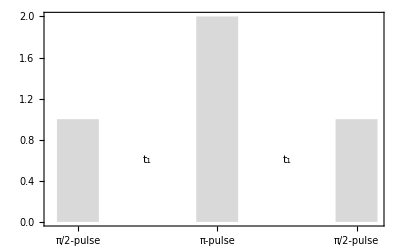

```mathematica
text$1 = Text[Style["t_1",Large],{2.5,0.6}];
text$2 = Text[Style["t_1",Large],{5.5,0.6}];
gr$ = Graphics[{text$1,text$2}];
pp$ = BarChart[{1,Missing[],Missing[],2,Missing[],Missing[],1},ChartStyle->{"Pastel",LightGray},ChartBaseStyle->EdgeForm[None],
ChartLabels->{"π/2-pulse","","","π-pulse","","","π/2-pulse"},LabelStyle->{FontSize->22},
Frame->{True,True,False,False},FrameTicksStyle->{Opacity[0],Opacity[1]},FrameStyle->Opacity[0],
(* Axes->{True,False},*) ImageSize->400];
DeleteCases[pp$,_Line?(Not@*FreeQ[_Offset]),All];
Show[pp$,gr$]
```

Density operator evolution

```mathematica
AbsoluteTiming[
(* Subscript[ρ, 0] is the density operator at thermal equilibrium *)
ρ0 = Iz1; 

(* Application of the first π/2-pulse with its phase set to {0, π/2, π, 3 π/2} *)
ρ1 = Pulse[ρ0,π/2,ϕ1,2]//Quiet;

(* A free-evolution period *)
ρ2 = FreeEvolution[ρ1,t1,2]//Quiet;

(* Application of the first refocusing π-pulse with its phase set to {0, π/2, π, 3 π/2} *)
ρ3 = 0;
dim = Dimensions[ρ2][[1]];
Monitor[
For[k=1,k<=dim,k++,
ρ = Pulse[ρ2[[k]],π,ϕ2,1];
AddTo[ρ3,ρ]],
Row[{ProgressIndicator[k,{1,dim}],NumberForm[(1.*k)/dim,{2,2}]},"  % ρ3 calculated = "]];
ρ3F = col$op[ρ3,2,1];

(* The second free-evolution period *)
ρ4 = 0;
dim = Dimensions[ρ3F][[1]];
Monitor[
For[k=1,k<=dim,k++,
ρ = FreeEvolution[ρ3F[[k]],t1,1];
AddTo[ρ4,ρ]],
Row[{ProgressIndicator[k,{1,dim}],NumberForm[(1.*k)/dim,{2,2}]},"  % ρ4 calculated = "]];
ρ4F = col$op[ρ4,2,1];

(* The second π/2-pulse to create multi-quantum coherence *)
ρ5 = 0;
dim = Dimensions[ρ4F][[1]];
Monitor[
For[k=1,k<=dim,k++,
ρ = Pulse[ρ4F[[k]],π/2,ϕ3,1];
AddTo[ρ5,ρ]],
Row[{ProgressIndicator[k,{1,dim}],NumberForm[(1.*k)/dim,{2,2}]},"  % ρ5 calculated = "]];
ρ5F = col$op[ρ5,2,1];][[1]]
```

6.04068

The general analytical expression of the density operator in the three pulse experiment is given by ρ5F. We will show how this expression can be used efficiently in understanding phase cycles that selectively generate specific coherence orders. 

**Note that the initial density operator ρ_0 is taken to be I_z1: given that the problem is symmetric with respect to the three spins, the density operator expressions for ρ_0 = I_z2 or I_z3 can be obtained by permutation of the indices in ρ5F.**

In general, three spin-1/2 particles can generate coherence orders in the range of ±3. By setting ϕ_1 = ϕ_2 = ϕ_3, one can selectively generate only even order coherence.

```mathematica
ρEvenQC = col$op[ρ5F/.{ϕ2->ϕ1, ϕ3->ϕ1},2,1]
```

Iz1 Cos[a12 t1] Cos[a13 t1]+2 Cos[a13 t1] Cos[ϕ1]^2 Mult[Ix1,Iy2] Sin[a12 t1]+2 Cos[a12 t1] Cos[ϕ1]^2 Mult[Ix1,Iy3] Sin[a13 t1]-4 Cos[ϕ1]^2 Mult[Iz1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1]-2 Cos[a13 t1] Mult[Iy1,Ix2] Sin[a12 t1] Sin[ϕ1]^2-2 Cos[a12 t1] Mult[Iy1,Ix3] Sin[a13 t1] Sin[ϕ1]^2-4 Mult[Iz1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2-Cos[a13 t1] Mult[Ix1,Ix2] Sin[a12 t1] Sin[2 ϕ1]+Cos[a13 t1] Mult[Iy1,Iy2] Sin[a12 t1] Sin[2 ϕ1]-Cos[a12 t1] Mult[Ix1,Ix3] Sin[a13 t1] Sin[2 ϕ1]+Cos[a12 t1] Mult[Iy1,Iy3] Sin[a13 t1] Sin[2 ϕ1]+2 Mult[Iz1,Ix2,Iy3] Sin[a12 t1] Sin[a13 t1] Sin[2 ϕ1]+2 Mult[Iz1,Iy2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[2 ϕ1]

One can inspect the above expression to find that it contains terms corresponding to 0 and ±2 coherence orders only. 
For example, the following terms from ρEvenQC 
A = -4 Cos[ϕ1]^2 Mult[Iz1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1]-4 Mult[Iz1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2 can be rewritten using spin raising and lowering operators as:

A = (Cos[ϕ1]^2 Mult[Iz1,(Ip2-Im2),(Ip3-Im3)]-Mult[Iz1,(Ip2+Im2),(Ip3+Im3)] Sin[ϕ1]^2)Sin[a12 t1] Sin[a13 t1]

Setting ϕ_1->0 and ϕ_1->π/2, the above expression transforms to

A1 = Mult[Iz1,(Ip2-Im2),(Ip3-Im3)]Sin[a12 t1] Sin[a13 t1], and
A2 = -Mult[Iz1,(Ip2+Im2),(Ip3+Im3)]Sin[a12 t1] Sin[a13 t1]

Now when we add or subtract A1 and A2, we can produce zero or double quantum coherence selectively, given by

A1 + A2 = -2×(Mult[Iz1,Ip2,Im3]+ Mult[Iz1,Im2,Ip3])Sin[a12 t1] Sin[a13 t1]

A1 - A2 = 2×(Mult[Iz1,Ip2,Ip3]+Mult[Iz1,Im2,Im3])Sin[a12 t1] Sin[a13 t1]

This is the basis of phase cycling in selecting quantum coherence of different orders in pulsed magnetic resonance experiments.

We apply the phase cycle to ρEvenQC to separate out 0 and ±2 coherence orders

```mathematica
zq$ = FullSimplify[Sum[(1)^(2*j)*ρEvenQC/.ϕ1->j*π/2,{j,0,1}]/2];
dq$ = FullSimplify[Sum[(-1)^j*ρEvenQC/.ϕ1->j*π/2,{j,0,1}]/2];
{Row[{"Zero quatum coherence signal = ",zq$}],Row[{"Double quantum coherence signal = ",dq$}]}
```

{Zero quatum coherence signal = Cos[a13 t1] (Iz1 Cos[a12 t1]+(Mult[Ix1,Iy2]-Mult[Iy1,Ix2]) Sin[a12 t1])+(Cos[a12 t1] (Mult[Ix1,Iy3]-Mult[Iy1,Ix3])-2 (Mult[Iz1,Ix2,Ix3]+Mult[Iz1,Iy2,Iy3]) Sin[a12 t1]) Sin[a13 t1],Double quantum coherence signal = Cos[a13 t1] (Mult[Ix1,Iy2]+Mult[Iy1,Ix2]) Sin[a12 t1]+(Cos[a12 t1] (Mult[Ix1,Iy3]+Mult[Iy1,Ix3])+2 (Mult[Iz1,Ix2,Ix3]-Mult[Iz1,Iy2,Iy3]) Sin[a12 t1]) Sin[a13 t1]}

Let’s plot the signals by assigning a_12->1 and a_13->2

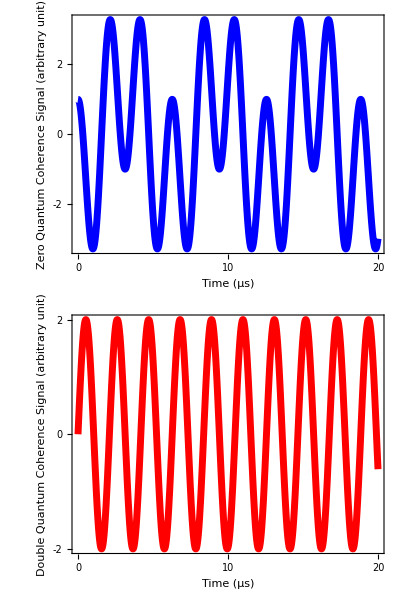

```mathematica
(* Assign values to the dipolar constants *)
dip$ = {a12->1., a13->2.}; (* in MHz *)
zq$N = zq$/.dip$;
dq$N = dq$/.dip$;

(* Plot ZQC *)
modPlotStyle={Frame->True,Axes->False,FrameStyle->Directive[Thick,Black],LabelStyle->Directive[16],FrameLabel->{Style["Time (μs)",20],Style[Row[{"Zero Quantum Coherence\n","Signal (arbitrary unit)"}],20]},ImageSize->500,PlotStyle->Directive[Thickness[0.01],Blue],FrameTicksStyle->Directive[18],ImagePadding->{{140,20},{60,20}}};
zqps$ = Plot[zq$N/.{ Ix1->1,Iy1->1,Iz1->1,Ix2->1,Ix3->1,Iy2->1,Iy3->1},{t1,0,20}, PlotRange->All, 
AxesOrigin->{0,-3},FrameTicks->{{{-2,0,2},None},{{0,10,20},None}}, Evaluate@modPlotStyle];

(* Plot DQC *)
modPlotStyle={Frame->True,Axes->False,FrameStyle->Directive[Thick,Black],LabelStyle->Directive[16],FrameLabel->{Style["Time (μs)",20],Style[Row[{"Double Quantum Coherence\n","Signal (arbitrary unit)"}],20]},ImageSize->500,PlotStyle->Directive[Thickness[0.01],Red],FrameTicksStyle->Directive[18],ImagePadding->{{140,20},{60,20}}};
dqps$ = Plot[dq$N/.{ Ix1->1,Iy1->1,Iz1->1,Ix2->1,Ix3->1,Iy2->1,Iy3->1},{t1,0,20}, PlotRange->All, 
AxesOrigin->{0,-3},FrameTicks->{{{-2,0,2},None},{{0,10,20},None}}, Evaluate@modPlotStyle];

(* Combine the plots *)
plots$ = {{zqps$},{dqps$}};
Grid[plots$]
```

The dipolar coupling constant is given by a_ij = ω_ij×(1-3*Cos^2[θ_ij]) and in the solid-state, to obtain a powder-averaged signal, one needs to average the signal over all possible values of θ_ij. We set ω_ij=52.04/r_ij^3, where r_ij is the distance between spin-i and spin-j and note that dCos[θ] = -Sin[θ]dθ. We further replace the integral with sum over discrete values of θ_ij to obtain the powder averaged zero and double quantum coherence signals as follows

```mathematica
Clear[zq$PA]
num$ = 40;t1$max = 10.;t1$step = 0.05;
norm$ = Sum[-Sin[θ12]*Sin[θ13]*Sin[θ23],{θ12,0,π,π/num$},{θ13,0,π,π/num$},{θ23,0,π,π/num$}];
AbsoluteTiming[zq$Sum= Sum[-zq$*Sin[θ12]*Sin[θ13]*Sin[θ23]/.{ Ix1->1,Iy1->1,Iz1->1,Ix2->1,Ix3->1,Iy2->1,Iy3->1}/.{a12->52.04/r12^3*(1-3*Cos[θ12]^2),a13->52.04/r13^3*(1-3*Cos[θ13]^2),a23->52.04/r23^3*(1-3*Cos[θ23]^2)}/.{r12->4., r13->3.,r23->3.},{θ12,0,π,π/num$},{θ13,0,π,π/num$},{θ23,0,π,π/num$}];
zq$PA = Table[zq$Sum/norm$,{t1,0,t1$max,t1$step}];][[1]]
```

26.5575

```mathematica
Clear[dq$PA]
num$ = 40;
AbsoluteTiming[dq$Sum= Sum[-dq$*Sin[θ12]*Sin[θ13]*Sin[θ23]/.{ Ix1->1,Iy1->1,Iz1->1,Ix2->1,Ix3->1,Iy2->1,Iy3->1}/.{a12->52.04/r12^3*(1-3*Cos[θ12]^2),a13->52.04/r13^3*(1-3*Cos[θ13]^2),a23->52.04/r23^3*(1-3*Cos[θ23]^2)}/.{r12->4., r13->3.,r23->3.},{θ12,0,π,π/num$},{θ13,0,π,π/num$},{θ23,0,π,π/num$}];
dq$PA = Table[dq$Sum/norm$,{t1,0,t1$max,t1$step}];][[1]]
```

25.7232

Let’s plot the powder averaged signals

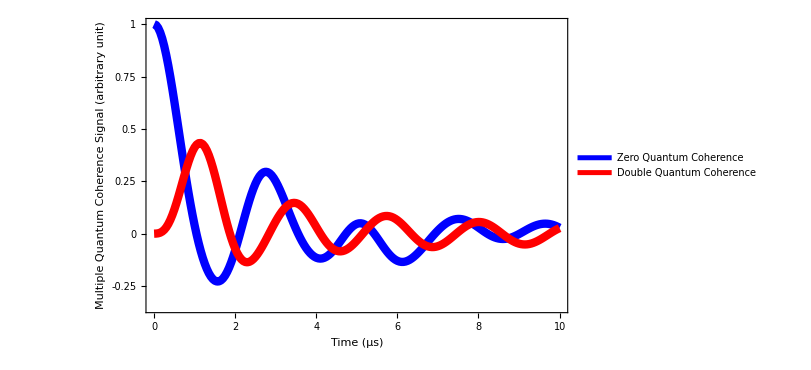

```mathematica
modPlotStyle={Frame->True,Axes->False,FrameStyle->Directive[Thick,Black],LabelStyle->Directive[16],FrameLabel->{Style["Time (μs)",24],Style[Row[{"Multiple Quantum Coherence\n","Signal (arbitrary unit)"}],24]},ImageSize->600,FrameTicksStyle->Directive[18],ImagePadding->{{140,20},{60,20}}};
time$Tab = Table[t1,{t1,0,t1$max,t1$step}];
ListPlot[{Transpose[{time$Tab,zq$PA}],Transpose[{time$Tab,dq$PA}]},Joined->True,PlotRange->All,AxesLabel->{"Time (μs)", "Signal Amplitude"},AxesOrigin->{0,-0.35},FrameTicks->{{{-0.25,0,0.25,0.5,0.75,1},None},{{0,2,4,6,8,10},None}},Evaluate@modPlotStyle,PlotLegends->Placed[LineLegend[{"Zero Quantum Coherence", "Double Quantum Coherence"}],{0.7, 0.8}],PlotStyle->{Directive[Thickness[0.01],Blue],Directive[Thickness[0.01],Red]}]
```

To select odd order quantum coherence, we set ϕ_1 = ϕ_2; ϕ_3 = ϕ_1+π/2

```mathematica
ρOddQC = col$op[ρ5F/.{ϕ2->ϕ1, ϕ3->ϕ1+π/2},2,1]
```

Iy1 Cos[a12 t1] Cos[a13 t1] Cos[ϕ1]+2 Cos[a13 t1] Cos[ϕ1] Mult[Iz1,Ix2] Sin[a12 t1]+2 Cos[a12 t1] Cos[ϕ1] Mult[Iz1,Ix3] Sin[a13 t1]-4 Cos[ϕ1]^3 Mult[Iy1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1]-Ix1 Cos[a12 t1] Cos[a13 t1] Sin[ϕ1]+2 Cos[a13 t1] Mult[Iz1,Iy2] Sin[a12 t1] Sin[ϕ1]+2 Cos[a12 t1] Mult[Iz1,Iy3] Sin[a13 t1] Sin[ϕ1]+4 Cos[ϕ1]^2 Mult[Ix1,Ix2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]-4 Cos[ϕ1]^2 Mult[Iy1,Ix2,Iy3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]-4 Cos[ϕ1]^2 Mult[Iy1,Iy2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]+4 Cos[ϕ1] Mult[Ix1,Ix2,Iy3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2+4 Cos[ϕ1] Mult[Ix1,Iy2,Ix3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2-4 Cos[ϕ1] Mult[Iy1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^2+4 Mult[Ix1,Iy2,Iy3] Sin[a12 t1] Sin[a13 t1] Sin[ϕ1]^3

We apply phase cycle to ρOddC to separate out ±3 coherence orders from ±1

```mathematica
tq$ = FullSimplify[Sum[(-1)^j*ρOddQC/.ϕ1->j*π/3+π/6,{j,0,5}]/6];
Row[{"Triple quantum coherence signal = ", tq$}]
```

Triple quantum coherence signal = (Mult[Ix1,Ix2,Ix3]-Mult[Ix1,Iy2,Iy3]-Mult[Iy1,Ix2,Iy3]-Mult[Iy1,Iy2,Ix3]) Sin[a12 t1] Sin[a13 t1]

```mathematica
Clear[tq$PA]
num$ = 40;t1$max = 10.;t1$step = 0.05;
norm$ = Sum[-Sin[θ12]*Sin[θ13]*Sin[θ23],{θ12,0,π,π/num$},{θ13,0,π,π/num$},{θ23,0,π,π/num$}];
AbsoluteTiming[tq$Sum= Sum[-tq$*Sin[θ12]*Sin[θ13]*Sin[θ23]/.{ Ix1->1,Iy1->1,Iz1->1,Ix2->1,Ix3->1,Iy2->1,Iy3->1}/.{a12->52.04/r12^3*(1-3*Cos[θ12]^2),a13->52.04/r13^3*(1-3*Cos[θ13]^2),a23->52.04/r23^3*(1-3*Cos[θ23]^2)}/.{r12->4., r13->3.,r23->3.},{θ12,0,π,π/num$},{θ13,0,π,π/num$},{θ23,0,π,π/num$}];
tq$PA = Table[tq$Sum/norm$,{t1,0,t1$max,t1$step}];][[1]]
```

20.9583

Let’s plot the powder averaged triple quantum coherence signal

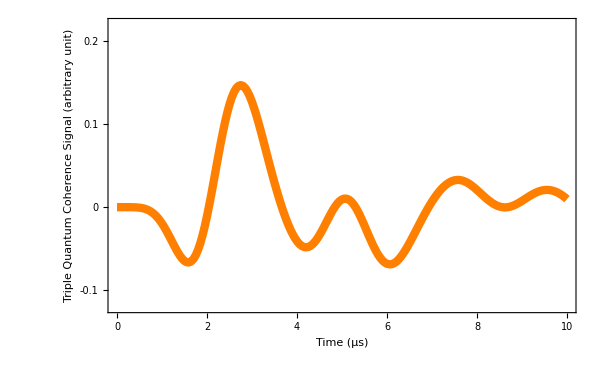

```mathematica
modPlotStyle={Frame->True,Axes->False,FrameStyle->Black,LabelStyle->Directive[16],FrameLabel->{Style["Time (μs)",24],Style[Row[{"Triple Quantum Coherence\n","Signal (arbitrary unit)"}],24]},ImageSize->600,PlotStyle->Directive[Thickness[0.01],Orange],FrameTicksStyle->Directive[18],ImagePadding->{{140,20},{60,20}}};
time$Tab = Table[t1,{t1,0,t1$max,t1$step}];
ListPlot[Transpose[{time$Tab,tq$PA}],Joined->True,PlotRange->{Automatic,{-0.12,0.22}},AxesOrigin->{0,-0.1},Evaluate@modPlotStyle,FrameTicks->{{{-0.1,0,0.1,0.2},None},{{0,2,4,6,8,10},None}}]
```

Note that simulating the triple quantum coherence signal using conventional numerical methods would require evaluating matrix exponentials of dimensions 8 × 8 at 6 × 201 × 41 × 41 = 2,027,286 points. This number corresponds to density operator evolution over three pulses and three free evolution periods, the time domain sampling, and averaging over θ_12 and θ_13.  As the number of spins and/or additional parameters increases, the total number of evaluation points grows rapidly, rendering the computation prohibitively expensive.

It is therefore advantageous to derive an analytical expression for the signal using UniDyn and subsequently export this expression to an efficient numerical platform, such as Python, for performing the required numerical simulations. [1-3]

#### References

Sinha Roy, A., Marohn, J.A. and Freed, J.H., An analysis of double-quantum coherence ESR in an N-spin system: Analytical expressions and predictions. J. Chem. Phys. (2024)

Sinha Roy, A., Assafa, T.E., Dzikovski, B., Joshi, N. and Freed, J.H., Rapid Analysis of DEER Signals Including Short Distances. J. Phys. Chem. Lett. (2024)

Sinha Roy, A., Tsay, K., Borbat, P.P., Destefano, A., Han, S., Srivastava, M. and Freed, J.H., Detection of Mutation-Induced Conformational Changes in an Intrinsically Disordered Protein by Double Quantum Coherence Electron Spin Resonance Methodology. J. Am. Chem. Soc. (2026)